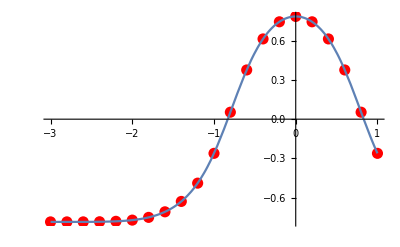

```mathematica
{a,b} ={-3.,1};
n = 21;
Δx = (b-a)/(n-1);
xs=Table[x,{x,a,b,Δx}];
xs =Range[a,b,Δx];
Length[xs];
f[x_]:= ArcTan[ Cos[x + Sin[x]]]
Show[
ListPlot[{xs,f[xs]}ᵀ, PlotStyle->{PointSize[0.02],Red}],
Plot[ f[x],{x,a,b}]
]
```